# Degree of Polarisation for the Barrel Detector

In this file you can calculate the degree of polarisation for the big barrel detector. Huge chunks of code are taken from the ‘Degree of Polarisation’ and the ‘Degree of Polarisation Batch Processing’ notebooks.

```mathematica
Needs["ErrorBarPlots`"]
```

## Data Import

Importing the data.

```mathematica
files=FileNames["*-degree-of-polarisation*.dat",NotebookDirectory[]] 
data=Import[#]&/@files;
```

{C:\Users\nicoe\ownCloud\! Exp Data\3 Output POVM Uncertainty\Experiment\Raw Data\measurements 23.11.2018\2018-11-23-1325-degree-of-polarisation.dat}

Specifying a position file to take the positions from. Only one at a time possible. So if measurement required a new position file it also needs a new notebook like this one you are reading right now.

```mathematica
position= Import[NotebookDirectory[]<>"2018-11-23-0900-degree-of-polarisation.pos","Table"]  [[1]][[;;;;4]];
```

## Definitions

## Data Cleaning & Error Calculation

```mathematica
countsPencilNormalized=Transpose[#[[5;;-1]]][[5]]&/@data;
countsPencil=Transpose[#[[5;;-1]]][[2]]&/@data;
```

Calculating the actual counts of the barrel detector. cts_barrel = norm_barrel * cts_pencil.

-Graphics-

```mathematica
counts=countsPencil[[#]]/countsPencilNormalized[[#]]&/@Range[Length[countsPencil]]
```

{{38.,24.,29.,33.,24.,24.,33.,20.,27.,27.,20.,27.,23.,30.,24.,25.,30.,20.,27.,25.,24.,18.,25.,24.,23.,32.,20.,30.,21.,24.,30.,23.,25.,28.,17.,31.,23.,19.,27.,27.,26.,25.,30.,35.,23.,12.,17.,40.,26.,22.,30.,28.,30.,29.,26.,47.,45.,31.,32.,45.,66.,31.,29.,45.,55.,43.,40.,45.,65.,37.,40.,60.,51.,16.,50.,51.,60.,54.,55.,47.,63.,53.,51.,61.,59.,63.,63.,64.,69.,63.,57.,61.,64.,58.,52.,68.,68.,57.,63.,62.}}

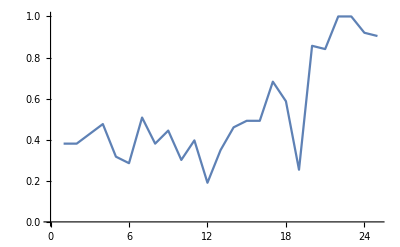

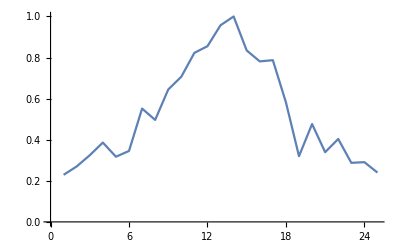

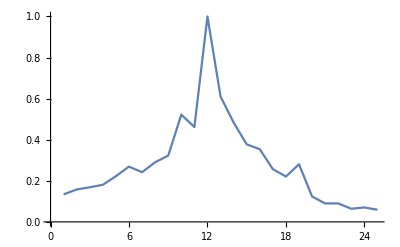

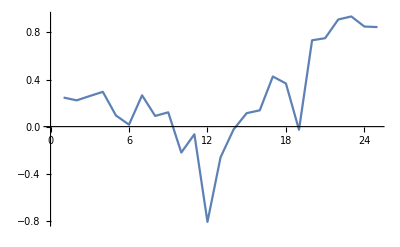

```mathematica
a=counts[[1]][[2;;;;4]];
b=countsPencil[[1]][[2;;;;4]];
c=countsPencilNormalized[[1]][[2;;;;4]];
a=a/Max[a];
b=b/Max[b];
c=c/Max[c];
ListLinePlot[a]
ListLinePlot[b]
ListLinePlot[c]
ListLinePlot[a-c]
```

```mathematica
countsPencil[[1]][[50]]
countsPencilNormalized[[1]][[50]]
countsPencil[[1]][[50]]/countsPencilNormalized[[1]][[50]]

countsPencil[[1]][[10]]
countsPencilNormalized[[1]][[10]]
countsPencil[[1]][[10]]/countsPencilNormalized[[1]][[10]]
```

184.375

8.38068

22.

62.5

2.31481

27.

```mathematica
ListLinePlot[countsBarrel[[1]]]
```

Part::partd: Part specification countsBarrel⟦1⟧ is longer than depth of object.

ListLinePlot::lpn: countsBarrel⟦1⟧ is not a list of numbers or pairs of numbers.

ListLinePlot[countsBarrel⟦1⟧]